# Combinatorics

This paclet is for the study of combinatorics. I am a combinatorialist. That means I study combinatorics.

The functions defined in the PeterBurbery`Combinatorics` context provide support for finding solutions to combinatorics-related problems.

```mathematica
Needs["PeterBurbery`Combinatorics`"]
```

## Indexes

PermutationIndex[perm] | gives the lexicographic index of permutation perm.
PermutationFromIndex[index,lengthInput] | returns the permutation of length lengthInput corresponding to the indexth permutation in lexicographic order.
SubsetIndex[list] | gives the index of subset list.
SubsetFromIndex[index,len] | returns a subset of length len with given index.

Computing the index or using the index to get the thing.

Find the index of a random permutation

```mathematica
PermutationIndex[Echo[PermutationList@RandomPermutation[9]]]
```

{2,6,9,1,4,8,3,5,7}

64843

Get the permutation:

```mathematica
PermutationFromIndex[%,9]
```

{2,6,9,1,4,8,3,5,7}

Here's a neat application of this function. We can use this to solve Project Euler Problem 24 Lexicographic Permutations. What is the millionth lexicographic permutation of the digits 0, 1, 2, 3, 4, 5, 6, 7, 8, and 9?

```mathematica
PermutationFromIndex[1000000(*a million is 10^6*), 10(*because Length[{0,1,2,3,4,5,6,7,8,,9}] is 10, not 9*)]
```

{3,8,9,4,10,2,6,5,7,1}

Now we need to subtract 1. 10 will become 9 and 1 will become 0.

```mathematica
PermutationFromIndex[1000000(*a million is 10^6*), 10(*because Length[{0,1,2,3,4,5,6,7,8,,9}] is 10, not 9*)]-1
```

{2,7,8,3,9,1,5,4,6,0}

Now we can use FromDigits.

```mathematica
FromDigits[PermutationFromIndex[1000000(*a million is 10^6*), 10(*because Length[{0,1,2,3,4,5,6,7,8,,9}] is 10, not 9*)]-1]
```

2783915460

And that's the answer!

Find a subset's index.

```mathematica
SubsetIndex[{2,4,6}]
```

29

Find the subset.

```mathematica
SubsetFromIndex[29,3]
```

{2,4,6}

## Central Binomial Coefficient

Compute the central binomial coefficient.

```mathematica
CentralBinomialCoefficient[54]
```

24857784491537440929618523018320

```mathematica
CentralBinomialCoefficient[n]
```

Binomial[2 n,n]

Find the generating function.

```mathematica
GeneratingFunction[CentralBinomialCoefficient[n],n,x]
```

1/(√(1-4 x))

Make a table of values.

```mathematica
Dataset[AssociationMap[<|"n"->CentralBinomialCoefficient[#]|>&][Range[21]]]
```

The digits of (2 10^n
10^n) for n=0, 1, … are

```mathematica
Dataset[AssociationMap[<|"n"->IntegerLength[CentralBinomialCoefficient[10^#]]|>&][Range[0,8]]]
```

These digits are converging to the digits of log_10 4.

```mathematica
N[Log[10,4],40]
```

0.6020599913279623904274777894489860535364

## Modified Central Binomial Coefficient

Let's look at the modified central binomial coefficient.

```mathematica
Dataset[AssociationMap[<|"n"->ModifiedCentralBinomialCoefficient[#]|>&][Range[0,21]]]
```

The generating function is  (1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)).

```mathematica
SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,9-1}]
```

126

This matches our output.

```mathematica
Dataset[AssociationMap[<|"n"->ModifiedCentralBinomialCoefficient[#],"seriesCoefficient"->SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,#-1}],"equal"->ModifiedCentralBinomialCoefficient[#]===SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,#-1}]|>&][Range[0,21]]]
```

If we start at 1, we will get all True instead of a False at 0.

```mathematica
Dataset[AssociationMap[<|"n"->ModifiedCentralBinomialCoefficient[#],"seriesCoefficient"->SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,#-1}],"equal"->ModifiedCentralBinomialCoefficient[#]===SeriesCoefficient[(1-4 x^2-√(1-4 x^2))/(2(2 x^3-x^2)),{x,0,#-1}]|>&][Range[2,21]]]
```

For more details, please visit A001405 on the OEIS.

## Derangements

A derangement is a permutation in which none of the objects appear in their "natural" (i.e., ordered) place. For example, the derangements of {1,2,3}:

```mathematica
MultisetPartialDerangements[{1,2,3}]
```

{{2,3,1},{3,1,2}}

Derangements of four elements:

```mathematica
MultisetPartialDerangements[{1,2,3,4}]
```

{{2,1,4,3},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,3,1,2},{4,3,2,1}}

The have no cycles of length one.

```mathematica
PermutationCycles/@MultisetPartialDerangements[{1,2,3,4}]
```

{Cycles[{{1,2},{3,4}}],Cycles[{{1,2,3,4}}],Cycles[{{1,2,4,3}}],Cycles[{{1,3,4,2}}],Cycles[{{1,3},{2,4}}],Cycles[{{1,3,2,4}}],Cycles[{{1,4,3,2}}],Cycles[{{1,4,2,3}}],Cycles[{{1,4},{2,3}}]}

```mathematica
Table[Apply[Identity][PermutationCycles[derangement]],{derangement,MultisetPartialDerangements[{1,2,3,4}]}]
```

{{{1,2},{3,4}},{{1,2,3,4}},{{1,2,4,3}},{{1,3,4,2}},{{1,3},{2,4}},{{1,3,2,4}},{{1,4,3,2}},{{1,4,2,3}},{{1,4},{2,3}}}

This is one way to find derangements.

```mathematica
MathWorldDerangements[l_List?ListQ]:=Module[{perms,support},perms=Permutations[l];support=Table[PermutationSupport[perm],{perm,perms}];Pick[perms,Table[Length[perm],{perm,support}],Length[l]]]
```

The support of a permutation perm is the list of integers that are not fixed by perm.

```mathematica
MathWorldDerangements[{1,2,3}]
```

{{2,3,1},{3,1,2}}

```mathematica
MathWorldDerangements[{1,2,3,4}]
```

{{2,1,4,3},{2,3,4,1},{2,4,1,3},{3,1,4,2},{3,4,1,2},{3,4,2,1},{4,1,2,3},{4,3,1,2},{4,3,2,1}}

A more efficient algorithm would not generate all the permutations and then pick the derangements, but instead just generate the derangements.

Make a random multiset of the hazel color rainbow palette. My eye-color is hazel.

```mathematica
hazelRainbowPalette=Table[LUVColor[RGBColor["#"<>color]],{color,{"c9c789","94c989","89c9b5","89a7c9","c989b9","c99089"}}]
```

{LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785]}

Let's find all the permutations where every element has moved. If an element stays in place, we name that a fixed point. A derangement is a permutation with 0 fixed points.

```mathematica
smallerset=RandomSample[hazelRainbowPalette,4]
```

{LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063]}

```mathematica
Rasterize[MultisetPartialDerangements[smallerset]]
```

-Graphics-

What is the length?

```mathematica
Length[MultisetPartialDerangements[smallerset]]
```

9

### Subfactorial

How can we compute the length faster and more efficiently? We can compute this with the subfactorial. The subfactorial is written ! n. The subfactorial is also called the derangement number for this reason. The nth subfactorial is the number of permutations of n objects in which no object appears in its natural place (i. e., "derangements").

```mathematica
Length[smallerset]
```

4

```mathematica
Subfactorial[Length[smallerset]]
```

9

Here's a table:

```mathematica
Subfactorial[Range[10]]
```

{0,1,2,9,44,265,1854,14833,133496,1334961}

Now we can find the number of derangements for a set with many elements.

```mathematica
Subfactorial[100]
```

34332795984163804765195977526776142032365783805375784983543400282685180793327632432791396429850988990237345920155783984828001486412574060553756854137069878601

We couldn't do this the other way.

```mathematica
MultisetPartialDerangements[Range[100]]
```

Permutations::fac: In Permutations[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}] there are at least 21 distinct elements in the input list, and the requested permutation lengths include one that is at least 21. The result cannot be computed because it has length at least 21 factorial, which is not a machine integer.

Permutations::argt: Permutations called with 0 arguments; 1 or 2 arguments are expected.

Permutations[]

Euler calculated the first ten terms of the subfactorial.

Here are representations of the subfactorial.

!n≡n!((-1)^k/(k!)k0n)

!n≡(-1)^(-k+n) k!(n
k)k0n

Here we use the incomplete gamma function for the subfactorial.

```mathematica
(n+1-1)/ⅇ;
```

```mathematica
RecurrenceTable[{subfactorial[1]==0,subfactorial[n]==n *subfactorial[n-1]+(-1)^n},subfactorial,{n,1,10}]
```

{0,1,2,9,44,265,1854,14833,133496,1334961}

We can solve for the representation of the subfactorial.

```mathematica
RSolve[{subfactorial[1]==0,subfactorial[n]==n *subfactorial[n-1]+(-1)^n},subfactorial,n]
```

{{subfactorial→Function[{n},Gamma[1+n,-1]/ⅇ]}}

For details, please visit OEIS A000166, Subfactorial or rencontres numbers, or derangements: number of permutations of n elements with no fixed points.

There is a connection with rook polynomials and the subfactorial. The subfactorial can be considered a special case of a restricted rooks problem.

One equation we can use is based on the nearest integer function, implemented in the Wolfram Language as round with support for rounding to the nearest even number to prevent a bias when you round up at 1/2, or 0.5. The notation is [x].

! n=[(n!)/ⅇ]

! n=[(n!+1)/ⅇ] for n>=1 and !n =⌊(ⅇ+ⅇ^-1)n!⌋-⌊ⅇ n!⌋ for n!=1.

Here is an integral form.

```mathematica
Integrate[x^n Exp[-(x+1)],{x,-1,Infinity}]
```

ConditionalExpression[Subfactorial[n], Re[n]>-1]

```mathematica
Refine[Integrate[x^n Exp[-(x+1)],{x,-1,Infinity}],Re[n]>-1]
```

Subfactorial[n]

Here is a continued fraction:

n!=(n!)/ⅇ+(-1^n)/(n+2-1/(n+3-2/(n+4-3/(n+5-…)))).

Let's look at the generating function.

```mathematica
GeneratingFunction[Subfactorial[n],n,x]
```

GeneratingFunction[Subfactorial[n],n,x]

Plot the sequence:

```mathematica
Rasterize[DiscretePlot[Subfactorial[n],{n,0,5}]](*I have to use Rasterize for the documentation to work.*)
```

-Graphics-

Plot over a subset of the complexes:

```mathematica
Rasterize[ComplexPlot3D[Subfactorial[z^2],{z,-2-2I,2+2I},PlotLegends->Automatic]]
```

-Graphics-

Series expansion at the origin:

```mathematica
Series[Subfactorial[ x], {x, 0, 2}]//Normal//FullSimplify
```

1-1/2 π x (-2 ⅈ+π x)+1/ⅇ x ((-ⅈ+π x) (π-ⅈ ExpIntegralEi[1])+x MeijerG[{{},{1,1}},{{0,0,0},{}},-1])

Series expansion at Infinitypaclet:ref/Infinity:

```mathematica
Series[Subfactorial[ x], {x, ∞, 2}]//Normal//FullSimplify
```

((-1)^x (-2+x))/x^2+1/144 ⅇ^(-1-x) √(π/2) x^(-3/2+x) (1+24 x (1+12 x))

Now that we can count a derangement, let's discuss partial derangements. We allow the number of fixed points to be a nonzero value.

```mathematica
randomSmallSet=RandomSample[hazelRainbowPalette,4]
```

{LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]}

Now we can find permutations with 2 fixed points. I have to apply Rasterize to build the documentation without errors.

```mathematica
Rasterize[MultisetPartialDerangements[randomSmallSet,2]]
```

-Graphics-

Now let's look at pure derangements of a small multiset.

```mathematica
smallMultiset=RandomChoice[hazelRainbowPalette,6]
```

{LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539]}

```mathematica
Rasterize[MultisetPartialDerangements[smallMultiset]]
```

-Graphics-

Let's count them.

```mathematica
Length[MultisetPartialDerangements[smallMultiset]]
```

29

To compute the number of partial derangements of a multiset, we integrate Laguerre polynomials.

```mathematica
EnumerateMultisetPartialDerangements[smallMultiset]
```

29

Let's compute the number of partial derangements for a multiset with too many elements to list the elements one by one.

```mathematica
randomMultiset=RandomChoice[hazelRainbowPalette,21]
```

{LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.7621596783781963, -0.3310170840401606, 0.08359158699165539],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.7930264647431842, 0.04643361077052847, 0.35301530185362595],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785]}

Count the derangements.

```mathematica
EnumerateMultisetPartialDerangements[randomMultiset]
```

46907596048

This is the same as having 0 fixed points.

```mathematica
EnumerateMultisetPartialDerangements[randomMultiset,0]
```

46907596048

Now let's see a small example of partial derangements of a multiset.

```mathematica
Rasterize[MultisetPartialDerangements[smallMultiset,2]]
```

-Graphics-

Let's find how many partial derangements with 2 fixed points there are.

```mathematica
Length[MultisetPartialDerangements[smallMultiset,2]]
```

57

Let's use Laguerre polynomials to compute this.

```mathematica
EnumerateMultisetPartialDerangements[smallMultiset,2]
```

57

Let's do a calculation for partial derangements where listing all permutations is infeasible.

Count partial derangements with 3 fixed points.

```mathematica
EnumerateMultisetPartialDerangements[randomMultiset,3]
```

827725861632

Let's do a smaller example again. This time, let's list all the elements of the set.

```mathematica
hazelRainbowPaletteSubset=RandomSample[hazelRainbowPalette,4]
```

{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.7605558615347562, -0.2762376510553367, 0.34253685287840063],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646]}

```mathematica
subsetRandomMultiset=RandomChoice[hazelRainbowPaletteSubset,{7}]
```

{LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785],LUVColor[0.648586156474065, 0.37271259045279787, -0.24310259911376647],LUVColor[0.6713375885659421, -0.17833924308420873, -0.26467794346262646],LUVColor[0.653613089342361, 0.39852960962686357, 0.09836345805217785]}

Let's find all the multiset partial derangements.

```mathematica
Rasterize[MultisetPartialDerangements[subsetRandomMultiset]]
```

-Graphics-

Here is the count.

```mathematica
EnumerateMultisetPartialDerangements[subsetRandomMultiset]
```

6

List partial derangements with 3 points, then take the length.

```mathematica
Rasterize[MultisetPartialDerangements[subsetRandomMultiset,3]]
```

-Graphics-

```mathematica
Length[MultisetPartialDerangements[subsetRandomMultiset,3]]
```

45

If we compute partials derangements with 3 fixed points, we will get 101 elements.

```mathematica
EnumerateMultisetPartialDerangements[subsetRandomMultiset,3]
```

45

I will limit the output to 20 this time. This is the third argument.

```mathematica
Rasterize[MultisetPartialDerangements[subsetRandomMultiset,3,20]]
```

-Graphics-

## Multichoose

There are four candies: gummy bears, gummy worms, chocolate bars,and marshmallows. There are three children named Peter, James, and Andrew (after the apostles from the Bible). How many ways can the four candies be distributed among the four children?

Let's list all the orderless combinations.

```mathematica
Rasterize[OrderlessCombinations[{"gummy-bears","gummy-worms","chocolate-bars","marshmallows"},{3}]]
```

-Graphics-

```mathematica
Length[OrderlessCombinations[{"gummy-bears","gummy-worms","chocolate-bars","marshmallows"},{3}]]
```

20

We can compute 4 multichoose 3, written as ((4
3)).

```mathematica
Multichoose[4,3]
```

20

There are ten candies: licorice, peppermint drops, lemon drops, truffles, gummy bears, gummy worms, chocolate bars, jelly beans, peanut butter cups, and marshmallows. There are four children named Peter, James, John, and Andrew. How many ways can the ten candies be distributed among the four children?

```mathematica
Length[OrderlessCombinations[{"licorice","peppermint-drops","lemon drops","truffles","gummy-bears","gummy-worms","chocolate-bars","jelly-beans","peanut-butter-cups","marshmallows"},{4}]]
```

715

We can compute 10 multichoose 4.

```mathematica
Multichoose[10,4]
```

715

Another way of entering it is like this is infix notation, written as ((10
4)).

```mathematica
10~Multichoose~4
```

715

We can also generate all the combinations and count them. Since there are a lot of combinations, I am not listing them all here and then using Length. I'm just going to use Length immediately.

```mathematica
Length@OrderlessCombinations[{"licorice","peppermint drops","lemon drops","truffles","gummy bears","gummy worms","chocolate bars","jelly beans","peanut butter cups","marshmallows"},{4}]
```

715

Get length four sets from a list of length two:

```mathematica
OrderlessCombinations[Range[2],{4}]
```

{{1,1,1,1},{1,1,1,2},{1,1,2,2},{1,2,2,2},{2,2,2,2}}

Elements need not be integers:

```mathematica
Rasterize[OrderlessCombinations[{"dog","cat","bird"},3]]
```

-Graphics-

## Orderless combinations of plain indistinguishable unmarked unlabeled elements

We could consider {"cat", "cat", "cat"} and {"dog", "dog", "dog"} as partly equal.

```mathematica
CanonicalMultiset[{"cat","cat","cat"}]
```

{1,1,1}

```mathematica
CanonicalMultiset[{"dog","dog","dog"}]
```

{1,1,1}

If we delete duplicates by CanonicalMultiset, we get fewer elements.

```mathematica
Rasterize[DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},3]]]
```

-Graphics-

```mathematica
Rasterize[CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},3]]]
```

-Graphics-

Here's what we would get something like.

```mathematica
OrderlessCombinationsOfUnmarkedElements[{"dog","cat","bird"},3]
```

{{1},{1,1},{1,2},{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

These produce the same output.

```mathematica
CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},3]]
```

{{1},{1,1},{1,2},{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

Let's compare the performance for a large set.

```mathematica
ResourceFunction["EchoPerformance"][CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},3]]]
```

Map  {0.0005623 s,7168 B}

{{1},{1,1},{1,2},{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

```mathematica
ResourceFunction["EchoPerformance"][OrderlessCombinationsOfUnmarkedElements[{"dog","cat","bird"},3]]
```

OrderlessCombinationsOfUnmarkedElements  {0.0003973 s,7280 B}

{{1},{1,1},{1,2},{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

```mathematica
ResourceFunction["EchoPerformance"][CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[{"dog","cat","bird"},7]];]
```

CompoundExpression  {0.0026763 s,40688 B}

```mathematica
ResourceFunction["EchoPerformance"][OrderlessCombinationsOfUnmarkedElements[{"dog","cat","bird"},7];]
```

CompoundExpression  {0.0021079 s,40272 B}

The definition of the function is significantly faster and uses significantly less memory.

```mathematica
ResourceFunction["EchoPerformance"][CanonicalMultiset/@DeleteDuplicatesBy[CanonicalMultiset][OrderlessCombinations[RandomWord["Noun",7],17]];]
```

CompoundExpression  {16.5169 s,148109320 B}

```mathematica
ResourceFunction["EchoPerformance"][OrderlessCombinationsOfUnmarkedElements[RandomWord["Noun",7],17];]
```

CompoundExpression  {9.02953 s,84408424 B}

## Monotonic function and weakly decreasing

In calculus, a function f defined on a subset of the real numbers (here we define subset as being allowed to be the whole set, that is the real numbers) with real values is called monotonic if and only if it is either entirely non-increasing, or entirely non-decreasing. That is, as per Figure 1, a function that increases monotonically does not exclusively have to increase, it simply must not decrease.

Figure 1: A monotonically non-decreasing function.

A function is called monotonically increasing (also increasing or non-decreasing) if for all x and y such that x ≤ y one has f(x) ≤ f(y), so f preserves the order (see Figure 1). Likewise, a function is called monotonically decreasing (also decreasing or non-increasing) if, whenever x ≤ y one has f(x) ≥ f(y), so that it reverses the order (see Figure 2).

Figure 2. A monotonically non-increasing function

If the order ≤ in the definition is replaced by the strict order <, one obtains a stronger requirement. A function with this property is called strictly increasing (also increasing). Again, by inverting the order symbol, one finds a corresponding property called strictly decreasing (also decreasing). A function with either property is called strictly monotone. Functions that are strictly monotone are one-to-one (because for x not equal to y, either x<y or x>y and so, by monotonicity, either, either f(x)<f(y) or f(x)>f(y), thus f(x)≠f(y).

To avoid ambiguity, the terms weakly monotone, weakly increasing, and weakly decreasing are often used to refer to non-strict monotonicity.

The terms "non-decreasing" and "non-increasing" should not be confused with the (much weaker) negative qualifications "not decreasing" and "not increasing". For example, the non-monotonic function shown in figure 3 first falls, then rises, then falls again. It is therefore not decreasing and not increasing, but it is neither non-decreasing nor non-increasing.

-Graphics-

Figure 3: A function that is not monotonic

Here are some useful functions for this.

```mathematica
Information[FunctionInjective]
```

```mathematica
Information[FunctionSurjective]
```

```mathematica
Information[FunctionMonotonicity]
```

x is weakly increasing:

```mathematica
FunctionMonotonicity[x,x]
```

1

-x is weakly decreasing:

```mathematica
FunctionMonotonicity[-x,x]
```

-1

x is strictly increasing:

```mathematica
FunctionMonotonicity[x,x,StrictInequalities->True]
```

1

-x is strictly decreasing:

```mathematica
FunctionMonotonicity[-x,x,StrictInequalities->True]
```

-1

To say {5,4,2,2} is weakly decreasing means that every element to the right of every element is less than or equal to it. For example, 4, 2, and 2 are all less than or equal to 5. 2 and 2 are less than or equal to 2. 2 is less than or equal to 2. If we specify strictly decreasing, equality is not allowed. We used equality with 2 and 2 here, so the sequence {5,4,2,2} is not strictly decreasing. {6,5,3,2} is strictly decreasing. The same logic applies to the terms weakly increasing and strictly increasing.

## Integer Partitions

In number theory and combinatorics, a partition of a non-negative integer n, also called an integer partition, is a way of writing n as a sum of positive integers. Two sums that differ only in the order of their summands are considered the same partition. (If order matters, the sum becomes a composition.) For example, 4 can be partitioned in five distinct ways:

```mathematica
Rasterize[Column[IntegerPartitions[4]]]
```

-Graphics-

The only partition of zero is the empty sum, having no parts.

The order-dependent composition 1+3 is the same partition as 3+1, and the two distinct compositions 1+2+1 and 1+1+2 represent the same partition as 2+1+1.

An individual summand in a partition is called a part. The number of partitions of n is given by the partition function p(n). So p(4)=5. The notation λ⊢n means that λ is a partition of n.

Partitions can be graphically represented with Young diagrams or Ferrers diagrams. They occur in a number of branches of mathematics and physics, including the study of symmetric polynomials and of the symmetric group and in group representation theory in general.

### Examples

The seven partitions of 5 are.

```mathematica
Rasterize[Column[Join[{5},Inactive[Plus]@@@Rest[IntegerPartitions[5]]]]]
```

-Graphics-

We can also use a list.

```mathematica
Rasterize[Column[IntegerPartitions[5]]]
```

-Graphics-

Some authors treat a partition as a decreasing sequence of summands, rather than an expression with plus signs. For example, the partition 2+2+1 might instead be written as the tuple (2,2,1) or even in the more compact form (2^2,1), where the superscript indicates the number of repetitions of a part.

This multiplicity notation for a partition can be written alternatively as 1^m_1 2^m_2 3^m_3..., where m_1 is the number of 1's, m_2 is the number of 2's, etc. (Components with m_i=0 may be omitted). For example, in this notation, the partitions of 5 are written

```mathematica
Counts/@IntegerPartitions[5]
```

{<|5→1|>,<|4→1,1→1|>,<|3→1,2→1|>,<|3→1,1→2|>,<|2→2,1→1|>,<|2→1,1→3|>,<|1→5|>}

```mathematica
KeyValueMap[f]/@Counts/@IntegerPartitions[5]
```

{{f[5,1]},{f[4,1],f[1,1]},{f[3,1],f[2,1]},{f[3,1],f[1,2]},{f[2,2],f[1,1]},{f[2,1],f[1,3]},{f[1,5]}}

```mathematica
KeyValueMap[Superscript]/@Counts/@IntegerPartitions[5]
```

{{5^1},{4^1,1^1},{3^1,2^1},{3^1,1^2},{2^2,1^1},{2^1,1^3},{1^5}}

```mathematica
Row[KeyValueMap[Superscript][#]]&/@Counts/@IntegerPartitions[5]
```

{5^1,4^11^1,3^12^1,3^11^2,2^21^1,2^11^3,1^5}

I have a function for this now.

Write a partition in plus notation.

```mathematica
PartitionPlusNotation[{2,2,1}]
```

2+2+1

Make a column of integer partitions for 5.

```mathematica
Rasterize[Column[PartitionPlusNotation/@IntegerPartitions[5]]]
```

-Graphics-

There is now a function for superscript notation too now.

```mathematica
PartitionSuperscriptNotation/@IntegerPartitions[5]
```

{5^1,4^11^1,3^12^1,3^11^2,2^21^1,2^11^3,1^5}

Write {2,2,1} in partition plus notation.

```mathematica
PartitionPlusNotation[{2,2,1}]
```

2+2+1

Go back to {2,2,1}:

```mathematica
FromPartitionPlusNotation[2+2+1]
```

{2,2,1}

List@@ would also work here:

```mathematica
List@@2+2+1
```

2+2+1

There is one time when List@@ will not work. That time is for a single integer.

```mathematica
List@@5
```

5

We wanted to return {5}, the way IntegerPartitions[5] does.

```mathematica
IntegerPartitions[5]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

We can use FromPartitionPlusNotation for this edge case.

```mathematica
PartitionPlusNotation/@IntegerPartitions[5]
```

{5,4+1,3+2,3+1+1,2+2+1,2+1+1+1,1+1+1+1+1}

```mathematica
FromPartitionPlusNotation/@PartitionPlusNotation/@IntegerPartitions[5]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

This is the inverse of PartitionPlusNotation.

```mathematica
FromPartitionPlusNotation/@PartitionPlusNotation/@IntegerPartitions[5]===IntegerPartitions[5]
```

True

Here are the integer partitions of 5:

```mathematica
IntegerPartitions[5]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

Here is a list of integer partitions in superscript notation:

```mathematica
PartitionSuperscriptNotation/@IntegerPartitions[5]
```

{5^1,4^11^1,3^12^1,3^11^2,2^21^1,2^11^3,1^5}

Go back to the integer partitions of 5:

```mathematica
FromPartitionSuperscriptNotation/@PartitionSuperscriptNotation/@IntegerPartitions[5]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

This is the inverse of PartitionSuperscriptNotation.

```mathematica
FromPartitionSuperscriptNotation/@PartitionSuperscriptNotation/@IntegerPartitions[5]===IntegerPartitions[5]
```

True

### Diagrammatic representations of partitions

There are two common diagrammatic methods to represent partitions: as Ferrers diagrams, named after Norman Macleod Ferrers, and  as Young diagrams, named after Alfred Young. Both have several possible conventions, here we use English notation, with diagrams aligned in the upper-left corner.

#### Ferrers diagram.

The partition 6+4+3+1 of the number 14 can be represented by the following diagram:

```mathematica
FerrersDiagram[{6,4,3,1}]
```

● | ● | ● | ● | ● | ●
● | ● | ● | ● |  | 
● | ● | ● |  |  | 
● |  |  |  |  |

```mathematica
Head[FerrersDiagram[{6,4,3,1}]]
```

Grid

The 14 circles are lined up in 4 rows, each having the size of a part of the partition. The diagrams for the 5 partitions of the number 4 are shown below:

```mathematica
Row[FerrersDiagram/@IntegerPartitions[4]]
```

● | ● | ● | ●● | ● | ●
● |  | ● | ●
● | ●● | ●
● | 
● | ●
●
●
●

#### Young diagram

An alternative visual representation of an integer partition is its Young diagram (often also called a Ferrers diagram). Rather than representing a partition with dots, as in the Ferrers diagram, the Young diagram uses boxes or squares. Thus, the Young diagram for the partition 5+4+1 is

```mathematica
Names["*Young*"]
```

{RandomYoungTableau,StandardYoungTableaux}

```mathematica
{5,4,1}
```

{5,4,1}

```mathematica
ConstantArray[1,#]&/@{5,4,1}
```

{{1,1,1,1,1},{1,1,1,1},{1}}

```mathematica
ConstantArray[1,#]&/@{5,4,1}
```

Consider the partition {5,4,2,2}.

```mathematica
Total[{5,4,2,2}]
```

13

Check if this is a weakly decreasing list of positive integers.

```mathematica
IntegerPartitionQ[{5,4,2,2}]
```

True

An integer partition is a multiset of positive integers and so not ordered. Therefore, any order can be used to represent it. Typically, the order chosen is weakly decreasing, as here; some people choose weakly increasing.

Here are the integer partitions of 13.

```mathematica
Information[IntegerPartitions]
```

These are all the partitions:

```mathematica
Rasterize[IntegerPartitions[13]]
```

-Graphics-

Between 1 and 4 parts—at most 4 parts:

```mathematica
Rasterize[IntegerPartitions[13,4]]
```

-Graphics-

Exactly 4 parts:

```mathematica
Rasterize[IntegerPartitions[13,{4}]]
```

-Graphics-

Between 1 and 4 parts:

```mathematica
Rasterize[IntegerPartitions[13,{1,4}]]
```

-Graphics-

Using only 5, 4, or 2:

```mathematica
Rasterize[IntegerPartitions[13,{1,4},{5,4,2}]]
```

-Graphics-

I'm curious if this returns the same as above.

```mathematica
Rasterize[IntegerPartitions[13,{1,4},{5,4,2,2}]]
```

-Graphics-

No it doesn't. We must use DeleteDuplicates.

Its not free of duplicates.

```mathematica
DuplicateFreeQ[IntegerPartitions[13,{1,4},{5,4,2,2}]]
```

False

Delete the duplicates.

```mathematica
DeleteDuplicates[IntegerPartitions[13,{1,4},{5,4,2,2}]]
```

{{2,2,4,5},{4,4,5}}

We can also limit the result to the a certain number of partitions.

Get the first 20 partitions.

```mathematica
Rasterize[IntegerPartitions[13,Infinity,All,20]]
```

-Graphics-

We can compute the number of partitions with PartitionsP.

```mathematica
Length[IntegerPartitions[13]]
```

101

```mathematica
PartitionsP[13]
```

101

Here's a table.

```mathematica
Dataset[AssociationMap[PartitionsP][Range[30]]]
```

Here's the asymptotic behavior:

```mathematica
DiscreteAsymptotic[PartitionsP[n],n->∞]
```

ⅇ^(√(2/3) √n π)/(4 √3 n)

```mathematica
DiscreteAsymptotic[PartitionsP[n],{n,∞,2}]
```

PartitionsP[n]

## Strict Partitions

A partition in which no part occurs more than once is called strict, or is said to be a partition into distinct parts. The function q(n) gives the number of these strict partitions of the given sum n.

Partitions of even length only:

```mathematica
IntegerPartitions[6,{2,Infinity,2}]
```

{{5,1},{4,2},{3,3},{3,1,1,1},{2,2,1,1},{1,1,1,1,1,1}}

Partitions of odd length:

```mathematica
IntegerPartitions[6,{1,Infinity,2}]
```

{{6},{4,1,1},{3,2,1},{2,2,2},{2,1,1,1,1}}

Partitions with only odd elements:

```mathematica
Solve[2n+1==target,n]
```

{{n→1/2 (-1+target)}}

```mathematica
SolveValues[2n+1==target,n]
```

{1/2 (-1+target)}

```mathematica
Identity@@SolveValues[2n+1==target,n]
```

1/2 (-1+target)

```mathematica
(target-1)/2;
```

```mathematica
IntegerPartitions[13,Infinity,Range[1,13,2]]
```

{{13},{11,1,1},{9,3,1},{9,1,1,1,1},{7,5,1},{7,3,3},{7,3,1,1,1},{7,1,1,1,1,1,1},{5,5,3},{5,5,1,1,1},{5,3,3,1,1},{5,3,1,1,1,1,1},{5,1,1,1,1,1,1,1,1},{3,3,3,3,1},{3,3,3,1,1,1,1},{3,3,1,1,1,1,1,1,1},{3,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1}}

There is a bijection between the partitions of a strictly positive integer into odd numbers and the partitions of a number into distinct parts.

Find the strict integer partitions of 16. List the partitions of 16 into distinct parts.

```mathematica
Rasterize[StrictIntegerPartitions[16]]
```

-Graphics-

A strict integer partition has no duplicate parts. For example, {5,3,1,1} has a duplicated 1. Therefore, {5,3,1,1} is not a strict integer partition. {6,4,2,1} has all unique parts so it is a strict integer partition.

The number of strict integer partitions is given by the partition function q(n).

```mathematica
q(n)
```

```mathematica
Length[StrictIntegerPartitions[16]]
```

32

```mathematica
PartitionsQ[16]
```

32

The function can generate large numbers of partitions quickly and efficiently:

```mathematica
PartitionsQ[80]
```

77312

```mathematica
ResourceFunction["EchoPerformance"][Length[StrictIntegerPartitions[80]]]
```

Length  {3.02163 s,26677952 B}

77312

Test this for the first 80 numbers:

```mathematica
AllTrue[Length[StrictIntegerPartitions[#]]===PartitionsQ[#]&][Range[80]]
```

True

For more details, please visit my Mathematica Stack Exchange post Design a function that gives all strict partitions of an integer.

## Ferrers Diagrams

Make a Ferrers diagram for every partition of 5.

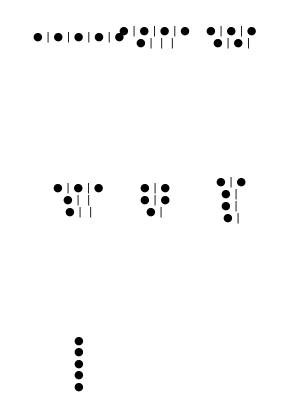

```mathematica
GraphicsGrid[Partition[FerrersDiagram/@IntegerPartitions[5],UpTo[3]]]
```

Rows 1 to 4 have 5, 4, 2, 2 dots:

```mathematica
FerrersDiagram[{5,4,2,2}]
```

● | ● | ● | ● | ●
● | ● | ● | ● | 
● | ● |  |  | 
● | ● |  |  |

Here is a random choice of one of the 204226 partitions of 50:

```mathematica
Framed@FerrersDiagram@RandomChoice[IntegerPartitions@50]
```

● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
● | ● | ● | ● | ● | ● | ● | ● | ● | ● | ●
● | ● | ● | ● | ● | ● |  |  |  |  | 
● | ● | ● | ● | ● | ● |  |  |  |  | 
● | ● | ● |  |  |  |  |  |  |  | 
● | ● |  |  |  |  |  |  |  |  | 
● | ● |  |  |  |  |  |  |  |  | 
● | ● |  |  |  |  |  |  |  |  | 
● | ● |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  | 
● |  |  |  |  |  |  |  |  |  |

Select from the list {5,6,7,8,9} those permutations that form a prime when concatenating the digits:

```mathematica
SelectPermutations[{5,6,7,8,9},PrimeQ@*FromDigits]
```

{{5,6,8,9,7},{5,7,6,8,9},{5,8,6,7,9},{5,8,9,6,7},{6,5,7,8,9},{6,7,5,8,9},{6,8,5,9,7},{6,9,8,5,7},{7,5,6,8,9},{7,5,8,6,9},{7,8,5,6,9},{8,6,5,7,9},{8,9,5,6,7},{8,9,6,5,7},{9,6,5,8,7},{9,6,8,5,7}}

Here are the numbers.

```mathematica
FromDigits/@SelectPermutations[{5,6,7,8,9},PrimeQ@*FromDigits]
```

{56897,57689,58679,58967,65789,67589,68597,69857,75689,75869,78569,86579,89567,89657,96587,96857}

Select permutations of length 3:

```mathematica
SelectPermutations[{5,6,7,8,9},{3},PrimeQ@*FromDigits]
```

{{5,6,9},{5,8,7},{6,5,9},{7,6,9},{8,5,7},{8,5,9},{9,6,7}}

Here are the numbers.

```mathematica
FromDigits/@SelectPermutations[{5,6,7,8,9},{3},PrimeQ@*FromDigits]
```

{569,587,659,769,857,859,967}

Select permutations with length 3—4:

```mathematica
SelectPermutations[{5,6,7,8,9},{3,4},PrimeQ@*FromDigits]
```

{{5,6,9},{5,8,7},{6,5,9},{7,6,9},{8,5,7},{8,5,9},{9,6,7},{5,6,8,9},{5,8,6,7},{5,8,6,9},{5,8,7,9},{5,8,9,7},{5,9,8,7},{6,8,5,7},{7,5,8,9},{8,5,9,7},{9,5,8,7},{9,8,5,7}}

Here are the numbers.

```mathematica
FromDigits/@SelectPermutations[{5,6,7,8,9},{3,4},PrimeQ@*FromDigits]
```

{569,587,659,769,857,859,967,5689,5867,5869,5879,5897,5987,6857,7589,8597,9587,9857}

Select permutations for which the first two elements and the last elements add up to the same value:

```mathematica
SelectPermutations[{1,2,3,4},Total[#[[1;;2]]]==Total[#[[3;;4]]]&]
```

{{1,4,2,3},{1,4,3,2},{2,3,1,4},{2,3,4,1},{3,2,1,4},{3,2,4,1},{4,1,2,3},{4,1,3,2}}

Select the first ten permutations of length 4 for which the elements add up to an odd number:

```mathematica
SelectPermutations[{1,2,3,4,5,6},{4},OddQ@*Total,10]
```

{{1,2,3,5},{1,2,4,6},{1,2,5,3},{1,2,6,4},{1,3,2,5},{1,3,4,5},{1,3,5,2},{1,3,5,4},{1,3,5,6},{1,3,6,5}}

Select polynomials for which the slope is 1 at x=0:

```mathematica
out=Total/@SelectPermutations[{x,4x,1,(x-2)^2},4,((D[Total[#],x])/.x->0)==1&]
```

{x,1+x,1+x,(-2+x)^2+5 x,(-2+x)^2+5 x,(-2+x)^2+5 x,(-2+x)^2+5 x,(-2+x)^2+5 x,(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x,1+(-2+x)^2+5 x}

Expand the polynomials.

```mathematica
Expand[out]
```

{x,1+x,1+x,4+x+x^2,4+x+x^2,4+x+x^2,4+x+x^2,4+x+x^2,4+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2,5+x+x^2}

There are really only three unique ones.

```mathematica
DeleteDuplicates[Expand[out]]
```

{x,1+x,4+x+x^2,5+x+x^2}

Make a graph of all of them.

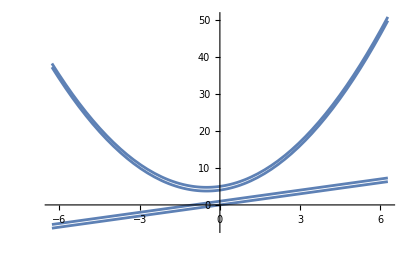

```mathematica
Plot[DeleteDuplicates[Expand[out]],{x,-2Pi,2Pi},PlotLegends->"Expressions"]
```

Confirm that the slope is indeed unity at x=0:

```mathematica
D[#,x]/.x->0&/@out
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Duplicated items are treated the same:

```mathematica
SelectPermutations[{6,7,7,7,8},{2},(Total[#]==14)&]
```

{{6,8},{7,7},{8,6}}

The main difference between SelectPermutations[list,crit] and Select[Permutations[list],crit] is the memory usage:

```mathematica
MaxMemoryUsed[result1=SelectPermutations[Range[3,13],6,Total[#]==24&];]
```

76800

Using Select and Permutations uses 500 times more memory:

```mathematica
MaxMemoryUsed[result2=Select[Permutations[Range[3,13],6],Total[#]==24&];]
```

37563192

Verify that the results are identical:

```mathematica
result1==result2
```

True

Head does not have to be List:

```mathematica
SelectPermutations[f[1,2,3,4,5],{2},((Plus@@#)==6&)]
```

{f[1,5],f[2,4],f[4,2],f[5,1]}

SelectPermutations might take longer as it is written in higher-level code as compared to the implementation of Permutations:

```mathematica
MaxMemoryUsed[time=AbsoluteTiming[result1=SelectPermutations[Range[3,13],6,Total[#]==24&];][[1]]];
Grid[{{"Time [sec]:",time},{"Memory usage [bytes]:",%}}]
```

Time [sec]: | 3.14873
Memory usage [bytes]: | 76800

Using the built-in functions is faster at the expense of 500× more memory:

```mathematica
MaxMemoryUsed[time=AbsoluteTiming[result2=Select[Permutations[Range[3,13],6],Total[#]==24&];][[1]]];
Grid[{{"Time [sec]:",time},{"Memory usage [bytes]:",%}}]
```

Time [sec]: | 0.898735
Memory usage [bytes]: | 37562680

Select subsets from {1,2,3,4,5} that add up to 10:

```mathematica
SelectSubsets[{1,2,3,4,5},EqualTo[10]@*Total]
```

{{1,4,5},{2,3,5},{1,2,3,4}}

Select subsets of length 2 to 4 that sum up to a prime:

```mathematica
SelectSubsets[{1,2,3,4,5},{2,4},PrimeQ@*Total]
```

{{1,2},{1,4},{2,3},{2,5},{3,4},{1,2,4},{2,4,5},{1,2,3,5},{1,3,4,5}}

Select all subsets of length 2 that add up to 6:

```mathematica
SelectSubsets[{1,2,3,4,5},{2},EqualTo[6]@*Total]
```

{{1,5},{2,4}}

Select all subsets that add up to 0:

```mathematica
SelectSubsets[{-3,-2,-1,0,1,2,3},All,EqualTo[0]@*Total]
```

{{},{0},{-3,3},{-2,2},{-1,1},{-3,0,3},{-3,1,2},{-2,-1,3},{-2,0,2},{-1,0,1},{-3,-2,2,3},{-3,-1,1,3},{-3,0,1,2},{-2,-1,0,3},{-2,-1,1,2},{-3,-2,0,2,3},{-3,-1,0,1,3},{-2,-1,0,1,2},{-3,-2,-1,1,2,3},{-3,-2,-1,0,1,2,3}}

Select all subsets of odd length that add up to a prime:

```mathematica
SelectSubsets[{-3,-2,-1,0,1,2,3},{1,7,2},PrimeQ@*Total]
```

{{-3},{-2},{2},{3},{-3,-2,0},{-3,-2,2},{-3,-2,3},{-3,-1,1},{-3,-1,2},{-3,0,1},{-3,2,3},{-2,-1,0},{-2,-1,1},{-2,1,3},{-2,2,3},{-1,0,3},{-1,1,2},{-1,1,3},{0,1,2},{0,2,3},{-3,-2,-1,0,1},{-3,-2,-1,0,3},{-3,-2,-1,1,2},{-3,-2,-1,1,3},{-3,-2,0,1,2},{-3,-1,1,2,3},{-3,0,1,2,3},{-2,-1,0,2,3},{-2,-1,1,2,3},{-1,0,1,2,3}}

Select the first 8 subsets that add up to a prime:

```mathematica
SelectSubsets[{1,2,3,4,5},All,PrimeQ@*Total,8]
```

{{2},{3},{5},{1,2},{1,4},{2,3},{2,5},{3,4}}

Find subsets that add up to 25:

```mathematica
SelectSubsets[Range[6,13],All,EqualTo[25]@*Total]
```

{{12,13},{6,7,12},{6,8,11},{6,9,10},{7,8,10}}

The main difference between Select and Subsets, and SelectSubsets is the amount of memory used:

```mathematica
MaxMemoryUsed[res1=SelectSubsets[Range[6,24],EqualTo[25]@*Total]]
```

62528

Compared to naive implementation, which requires roughly a 1000 times more memory:

```mathematica
MaxMemoryUsed[res2=Select[Subsets[Range[6,24]],EqualTo[25]@*Total]]
```

65071816

Verify the result is the same:

```mathematica
res1===res2
```

True

With a criterion that is a tautology, SelectSubsets and Subsets give the same results:

```mathematica
SelectSubsets[Range[5],True&]==Subsets[Range[5]]
```

True

SelectSubsets might not be able to return the number of elements that are requested:

```mathematica
SelectSubsets[Range[5],All,EqualTo[8]@*Total,5]
```

{{3,5},{1,2,5},{1,3,4}}

Find subsets that add up to 0:

```mathematica
sets=SelectSubsets[Range[-7,7],All,EqualTo[0]@*Total];
Short[sets]
```

{{},{0},«1517»,{-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7}}

Visualize the lengths of the lists:

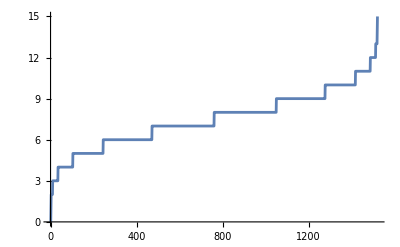

```mathematica
ListPlot[Length/@sets,Joined->True]
```

Find out for which 2-tuple the sum is a prime:

```mathematica
SelectTuples[Range[10],2,PrimeQ@*Total]
```

{{1,1},{1,2},{1,4},{1,6},{1,10},{2,1},{2,3},{2,5},{2,9},{3,2},{3,4},{3,8},{3,10},{4,1},{4,3},{4,7},{4,9},{5,2},{5,6},{5,8},{6,1},{6,5},{6,7},{7,4},{7,6},{7,10},{8,3},{8,5},{8,9},{9,2},{9,4},{9,8},{9,10},{10,1},{10,3},{10,7},{10,9}}

Only get the first five:

```mathematica
SelectTuples[Range[10],2,PrimeQ@*Total,5]
```

{{1,1},{1,2},{1,4},{1,6},{1,10}}

Find the first 15 three-letter palindromic lists:

```mathematica
SelectTuples[CharacterRange["a","e"],3,PalindromeQ@*StringJoin,15]
```

{{a,a,a},{a,b,a},{a,c,a},{a,d,a},{a,e,a},{b,a,b},{b,b,b},{b,c,b},{b,d,b},{b,e,b},{c,a,c},{c,b,c},{c,c,c},{c,d,c},{c,e,c}}

Find vectors for which the norm is an integer:

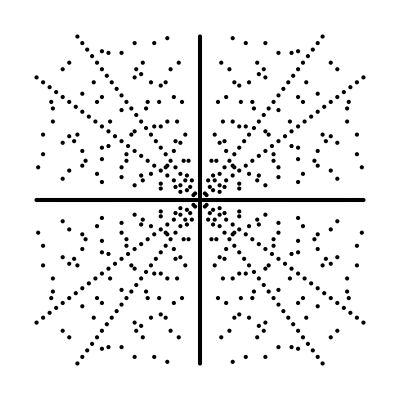

```mathematica
SelectTuples[Range[-100,100],2,IntegerQ@*Norm]//Point//Graphics
```

The main difference between Select and Tuples and SelectTuples is the amount of memory used:

```mathematica
MaxMemoryUsed[SelectTuples[Range[10],5,EqualTo[30]@*Total]]
```

1049416

Compared to naive implementation:

```mathematica
MaxMemoryUsed[Select[Tuples[Range[10],5],EqualTo[30]@*Total]]
```

21711208

The length of the results might be smaller than the argument m:

```mathematica
SelectTuples[{-1,0,1},3,EqualTo[1]@*Norm,10]
```

{{-1,0,0},{0,-1,0},{0,0,-1},{0,0,1},{0,1,0},{1,0,0}}

I got kind of confused with this.

Combinatorica's Eulerian[n,k] gives the number of permutations of length n with k runs.

This function uses a different index for k.

If you have EulerianNumber[n,k], do Eulerian[n,k-1].

If you have Eulerian[n,k], do EulerianNumber[n,k+1].

This also affects the definition of other related functions like EulerianCatalanNumber.

One interpretation of the Eulerian Catalan number is "Twice the number of permutations of {1,2,...,2n} with n ascents".

```mathematica
Dataset[AssociationMap[<|"n"->EulerianCatalanNumber[#]|>&][Range[0,21]]]
```

The table of Eulerian numbers up to 10:

```mathematica
Grid[Table[EulerianNumber[n,k],{n,10},{k,n}],Frame->All]
```

1 |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  | 
1 | 4 | 1 |  |  |  |  |  |  | 
1 | 11 | 11 | 1 |  |  |  |  |  | 
1 | 26 | 66 | 26 | 1 |  |  |  |  | 
1 | 57 | 302 | 302 | 57 | 1 |  |  |  | 
1 | 120 | 1191 | 2416 | 1191 | 120 | 1 |  |  | 
1 | 247 | 4293 | 15619 | 15619 | 4293 | 247 | 1 |  | 
1 | 502 | 14608 | 88234 | 156190 | 88234 | 14608 | 502 | 1 | 
1 | 1013 | 47840 | 455192 | 1310354 | 1310354 | 455192 | 47840 | 1013 | 1

Eulerian numbers of the second kind are written something like ⟨⟨n
m⟩⟩.

The first 9 rows of the triangle of Eulerian numbers of the second kind:

```mathematica
Grid[Table[EulerianNumberOfTheSecondKind[n,k],{n,9},{k,n}],Frame->All]
```

0 |  |  |  |  |  |  |  | 
2 | 0 |  |  |  |  |  |  | 
8 | 6 | 0 |  |  |  |  |  | 
22 | 58 | 24 | 0 |  |  |  |  | 
52 | 328 | 444 | 120 | 0 |  |  |  | 
114 | 1452 | 4400 | 3708 | 720 | 0 |  |  | 
240 | 5610 | 32120 | 58140 | 33984 | 5040 | 0 |  | 
494 | 19950 | 195800 | 644020 | 785304 | 341136 | 40320 | 0 | 
1004 | 67260 | 1062500 | 5765500 | 12440064 | 11026296 | 3733920 | 362880 | 0

The first 14 rows of the Narayana triangle read as follows:

```mathematica
Grid[Table[NarayanaNumber[n,k],{n,14},{k,n}],Frame->All]
```

1 |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | 1 |  |  |  |  |  |  |  |  |  |  |  | 
1 | 3 | 1 |  |  |  |  |  |  |  |  |  |  | 
1 | 6 | 6 | 1 |  |  |  |  |  |  |  |  |  | 
1 | 10 | 20 | 10 | 1 |  |  |  |  |  |  |  |  | 
1 | 15 | 50 | 50 | 15 | 1 |  |  |  |  |  |  |  | 
1 | 21 | 105 | 175 | 105 | 21 | 1 |  |  |  |  |  |  | 
1 | 28 | 196 | 490 | 490 | 196 | 28 | 1 |  |  |  |  |  | 
1 | 36 | 336 | 1176 | 1764 | 1176 | 336 | 36 | 1 |  |  |  |  | 
1 | 45 | 540 | 2520 | 5292 | 5292 | 2520 | 540 | 45 | 1 |  |  |  | 
1 | 55 | 825 | 4950 | 13860 | 19404 | 13860 | 4950 | 825 | 55 | 1 |  |  | 
1 | 66 | 1210 | 9075 | 32670 | 60984 | 60984 | 32670 | 9075 | 1210 | 66 | 1 |  | 
1 | 78 | 1716 | 15730 | 70785 | 169884 | 226512 | 169884 | 70785 | 15730 | 1716 | 78 | 1 | 
1 | 91 | 2366 | 26026 | 143143 | 429429 | 736164 | 736164 | 429429 | 143143 | 26026 | 2366 | 91 | 1

Make a table of signed and unsigned Lah numbers.

```mathematica
Grid[Table[SignedLahNumber[n,k],{n,9},{k,n}],Frame->All]
```

-1 |  |  |  |  |  |  |  | 
2 | 1 |  |  |  |  |  |  | 
-6 | -6 | -1 |  |  |  |  |  | 
24 | 36 | 12 | 1 |  |  |  |  | 
-120 | -240 | -120 | -20 | -1 |  |  |  | 
720 | 1800 | 1200 | 300 | 30 | 1 |  |  | 
-5040 | -15120 | -12600 | -4200 | -630 | -42 | -1 |  | 
40320 | 141120 | 141120 | 58800 | 11760 | 1176 | 56 | 1 | 
-362880 | -1451520 | -1693440 | -846720 | -211680 | -28224 | -2016 | -72 | -1

```mathematica
Grid[Table[UnsignedLahNumber[n,k],{n,9},{k,n}],Frame->All]
```

1 |  |  |  |  |  |  |  | 
2 | 1 |  |  |  |  |  |  | 
6 | 6 | 1 |  |  |  |  |  | 
24 | 36 | 12 | 1 |  |  |  |  | 
120 | 240 | 120 | 20 | 1 |  |  |  | 
720 | 1800 | 1200 | 300 | 30 | 1 |  |  | 
5040 | 15120 | 12600 | 4200 | 630 | 42 | 1 |  | 
40320 | 141120 | 141120 | 58800 | 11760 | 1176 | 56 | 1 | 
362880 | 1451520 | 1693440 | 846720 | 211680 | 28224 | 2016 | 72 | 1

Find the sum of even-valued Fibonacci numbers less than 4 million.

We aren't counting 4 million, so we need to find the inverse of 4000000-1, or 3999999.

Compute the inverse Fibonacci of 4 million.

```mathematica
InverseFibonacci[3999999]
```

Root33.3Root[{-3999999+Fibonacci[#1]&,33.2629474}]33.26294740017785

Now we can solve Project Euler Problem 2 Even Fibonacci Numbers.

```mathematica
Fibonacci[Range[Floor[InverseFibonacci[3999999]]]]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040,1346269,2178309,3524578}

```mathematica
Select[EvenQ][Fibonacci[Range[Floor[InverseFibonacci[3999999]]]]]
```

{2,8,34,144,610,2584,10946,46368,196418,832040,3524578}

```mathematica
Total[Select[EvenQ][Fibonacci[Range[Floor[InverseFibonacci[3999999]]]]]]
```

4613732

That's the answer.

Let's work through the examples from the Wolfram Challenge Next Permutation.

```mathematica
NextPermutation[{2,3,1}]
```

{3,1,2}

Here are more examples.

```mathematica
NextPermutation[{3,2,1}]
```

{1,2,3}

```mathematica
NextPermutation[{1,2,4,5}]
```

{1,2,5,4}

```mathematica
NextPermutation[{4,5,1,0}]
```

{5,0,1,4}

For some reason, although I have a function that can compute the next permutation, I have not solved this Wolfram Challenge.

Consider the permutation:

```mathematica
p={2,8,1,5,4,7,6,3,9};
```

Its ascents are at the indices 1, 3, 5, 8, corresponding to 2 < 8, 1 < 5, 4 < 7, 3 < 9:

```mathematica
PermutationAscents@p
```

{1,3,5,8}

The descents follow easily:

```mathematica
Reverse[Length@p-PermutationAscents@Reverse@p]
```

{2,4,6,7}

There is also a function for this.

```mathematica
PermutationDescents[p]
```

{2,4,6,7}

A triangular table of Gauss factorials up to 7::

```mathematica
Table[GaussFactorial[n,k],{n,7},{k,n}]
```

{{1},{2,1},{6,3,2},{24,3,8,3},{120,15,40,15,24},{720,15,40,15,144,5},{5040,105,280,105,1008,35,720}}

Make a grid with a frame:

```mathematica
Grid[Table[GaussFactorial[n,k],{n,7},{k,n}],Frame->All]
```

1 |  |  |  |  |  | 
2 | 1 |  |  |  |  | 
6 | 3 | 2 |  |  |  | 
24 | 3 | 8 | 3 |  |  | 
120 | 15 | 40 | 15 | 24 |  | 
720 | 15 | 40 | 15 | 144 | 5 | 
5040 | 105 | 280 | 105 | 1008 | 35 | 720

Phitorial of 10:

```mathematica
Phitorial[10]
```

189

Project Euler Problem 754 Product of Gauss Factorials states, "The Gauss Factorial of a number n is defined as the product of all positive numbers <=n  that are relatively prime to n. For example, g(10)=1 3 7 9=189. Also, we define G(n)=∏_(i=1)^n g(i). You are given G(10)=23044331520000. Find G(10^8). Give your answer modulo 1000000007."

Compute the products of the first 10 phitorials to verify the statement G(10)=23044331520000:

```mathematica
EchoTiming@Product[Phitorial[n],{n,10}]
```

0.0002024

23044331520000

Compute the phitorial product up to 10^4:

```mathematica
EchoTiming[Product[Phitorial[n],{n,10^4}]]
```

43.6647

Compute the answer mod 1000000007:

```mathematica
Mod[%,1000000007]
```

517055464

Product of primes up to 20:

```mathematica
Primorial[20]
```

9699690

Product of primes up to 54:

```mathematica
Primorial[54]
```

32589158477190044730

Compute the primorial 23#:

```mathematica
Primorial[23]
```

223092870

Compute a list of the first 15 primorials:

```mathematica
Primorial[Range[15]]
```

{1,2,6,6,30,30,210,210,210,210,2310,2310,30030,30030,30030}

Compare with the definition:

```mathematica
With[{k=7},Product[Prime[j],{j,1,PrimePi[k]}]==Primorial[k]]
```

True

The resource function ChebyshevTheta is the logarithm of the primorial:

```mathematica
With[{k=7},Exp[ResourceFunction["ChebyshevTheta"][k]]==Primorial[k]]
```

True

Evaluate the infinite primorial:

```mathematica
Product[Prime[k],{k,1,∞},Regularization->"Dirichlet"]
```

4 π^2

```mathematica
Primorial[∞]
```

4 π^2

Compare the growth rate of the primorial versus factorial:

```mathematica
Rasterize[DiscretePlot[{Primorial[n],Factorial[n]},{n,1,50},ScalingFunctions->"Log",PlotLegends->{"n#","n!"}]]
```

-Graphics-

Plot the differences between the factorial and the primorial up to n:

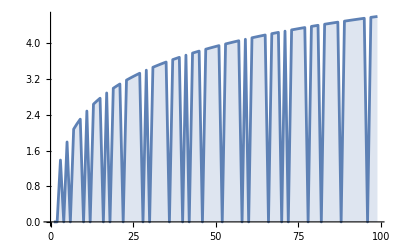

```mathematica
ListLinePlot[Differences[Table[Log[(n!)/Primorial[n]],{n,1,100,1}]],]
```

```mathematica
?LucasNumberU1
```

U_n(2,-1) represents the Pell numbers:

```mathematica
EchoTiming[LucasNumberU1[Range[21],2,-1]]
```

0.0000281

{1,2,5,12,29,70,169,408,985,2378,5741,13860,33461,80782,195025,470832,1136689,2744210,6625109,15994428,38613965}

You can also do the Pell numbers with LinearRecurrence:

```mathematica
LinearRecurrence[{2,1},{0,1},21]
```

{0,1,2,5,12,29,70,169,408,985,2378,5741,13860,33461,80782,195025,470832,1136689,2744210,6625109,15994428}

Find a linear recurrence:

```mathematica
FindLinearRecurrence[EchoTiming[LucasNumberU1[Range[21],2,-1]]]
```

0.0001767

{2,1}

Generate a linear recurrence:

```mathematica
LinearRecurrence[FindLinearRecurrence[EchoTiming[LucasNumberU1[Range[21],2,-1]]],Take[LucasNumberU1[Range[2],2,-1],2],10]
```

0.0000285

{1,2,5,12,29,70,169,408,985,2378}

We can also find a Fibonacci function:

```mathematica
FindSequenceFunction[LucasNumberU1[Range[21],2,-1]]
```

Fibonacci[#1,2]&

U_n(1,-2) represents the Jacobsthal numbers:

```mathematica
EchoTiming[LucasNumberU1[Range[21],1,-2]]
```

0.0000269

{1,1,3,5,11,21,43,85,171,341,683,1365,2731,5461,10923,21845,43691,87381,174763,349525,699051}

We can find a pattern:

```mathematica
FindSequenceFunction[LucasNumberU1[Range[21],1,-2]]
```

1/3 (-(-1)^#1+2^#1)&

Generate a new array:

```mathematica
Array[FindSequenceFunction[LucasNumberU1[Range[21],1,-2]],21]
```

{1,1,3,5,11,21,43,85,171,341,683,1365,2731,5461,10923,21845,43691,87381,174763,349525,699051}

U_n(3,2) represents the Mersenne numbers:

```mathematica
EchoTiming[LucasNumberU1[Range[21],3,2]]
```

0.0000259

{1,3,7,15,31,63,127,255,511,1023,2047,4095,8191,16383,32767,65535,131071,262143,524287,1048575,2097151}

U_n(6,1) represents the square roots of the square triangular numbers:

```mathematica
EchoTiming[LucasNumberU1[Range[21],6,1]]
```

0.0000271

{1,6,35,204,1189,6930,40391,235416,1372105,7997214,46611179,271669860,1583407981,9228778026,53789260175,313506783024,1827251437969,10650001844790,62072759630771,361786555939836,2108646576008245}

U_n(x,-1) represents the Fibonacci polynomials:

```mathematica
Expand[LucasNumberU1[Range[7],x,-1]]
```

{1,x,1+x^2,2 x+x^3,1+3 x^2+x^4,3 x+4 x^3+x^5,1+6 x^2+5 x^4+x^6}

Verify the statement up to 7:

```mathematica
SameQ[Expand[LucasNumberU1[Range[7],x,-1]],Fibonacci[Range[7],x]]
```

True

U_n(2x,1) represents Chebyshev polynomials of the second kind:

```mathematica
Expand[LucasNumberU1[Range[7],2x,1]]
```

{1,2 x,-1+4 x^2,-4 x+8 x^3,1-12 x^2+16 x^4,6 x-32 x^3+32 x^5,-1+24 x^2-80 x^4+64 x^6}

Verify this statement:

```mathematica
SameQ[Expand[LucasNumberU1[Range[1+1,7+1],2x,1]],ChebyshevU[Range[1+0,7+0],x]]
```

True

U_n(x+1,x) represents repunits in base x:

```mathematica
Expand[LucasNumberU1[1+Range[7],x+1,x]]
```

{1+x,1+x+x^2,1+x+x^2+x^3,1+x+x^2+x^3+x^4,1+x+x^2+x^3+x^4+x^5,1+x+x^2+x^3+x^4+x^5+x^6,1+x+x^2+x^3+x^4+x^5+x^6+x^7}

The first 21 Lucas numbers:

```mathematica
LucasNumberV2[Range[21],1,-1]
```

{1,3,4,7,11,18,29,47,76,123,199,322,521,843,1364,2207,3571,5778,9349,15127,24476}

Compare the function to LucasL:

```mathematica
LucasL[Range[21]]===LucasNumberV2[Range[21],1,-1]
```

True

V_n(2,-1) gives the Pell-Lucas numbers (companion Pell numbers):

```mathematica
LucasNumberV2[Range[21],2,-1]
```

{2,6,14,34,82,198,478,1154,2786,6726,16238,39202,94642,228486,551614,1331714,3215042,7761798,18738638,45239074,109216786}

V_n(1,-2) gives the Jacobsthal-Lucas numbers:

```mathematica
LucasNumberV2[Range[21],1,-2]
```

{1,5,7,17,31,65,127,257,511,1025,2047,4097,8191,16385,32767,65537,131071,262145,524287,1048577,2097151}

V_n(3,2) gives number of the form 2^n+1, which includes the Fermat numbers:

```mathematica
LucasNumberV2[Range[21],3,2]
```

{3,5,9,17,33,65,129,257,513,1025,2049,4097,8193,16385,32769,65537,131073,262145,524289,1048577,2097153}

V_n(x,-1) gives the Lucas polynomials:

```mathematica
Expand[LucasNumberV2[Range[7],x,-1]]
```

{x,2+x^2,3 x+x^3,2+4 x^2+x^4,5 x+5 x^3+x^5,2+9 x^2+6 x^4+x^6,7 x+14 x^3+7 x^5+x^7}

Let's compare this to LucasL:

```mathematica
Expand[LucasNumberV2[Range[7],x,-1]]===LucasL[Range[7],x]
```

True

V_n(2x,1) gives Chebyshev polynomials of first kind multiplied by 2:

```mathematica
Expand[LucasNumberV2[Range[7],2x,1]]
```

{2 x,-2+4 x^2,-6 x+8 x^3,2-16 x^2+16 x^4,10 x-40 x^3+32 x^5,-2+36 x^2-96 x^4+64 x^6,-14 x+112 x^3-224 x^5+128 x^7}

Test this statement:

```mathematica
Expand[LucasNumberV2[Range[7],2x,1]]===(Expand[2*#]&/@ChebyshevT[Range[7],x])
```

True

V_n(x+1,x) gives x^n+1:

```mathematica
Expand[LucasNumberV2[Range[7],x+1,x]]
```

{1+x,1+x^2,1+x^3,1+x^4,1+x^5,1+x^6,1+x^7}

Test this statement:

```mathematica
Expand[LucasNumberV2[Range[7],x+1,x]]===Table[x^n+1,{n,7}]
```

True

Evaluate the q-exponential.

Evaluate numerically:

```mathematica
QExponential[3.4,1]
```

29.9641

Change q from 1 to 2.

```mathematica
QExponential[17/5,2]
```

10.5982940927869

Ask for 40 digits of precision.

```mathematica
QExponential[17/5,2,40]
```

10.59829409278693878204709467134680730862

Evaluate the q-multinomial.

Evaluate numerically:

```mathematica
QMultinomial[1,2,1,E]
```

QGamma[5,ⅇ]/(1+ⅇ)

```mathematica
N[QMultinomial[1,2,1,E]]
```

346.47

```mathematica
N[QMultinomial[1,2,1,E],40]
```

346.4698018921381259525335487344495385551

Find the period of the decimal representation of a rational number.

Find the period of the repetend of the repeating decimal corresponding to  1/983.

```mathematica
RationalNumberRepeatingDecimalPeriod[1/983]
```

982

3/2 has a period of 0.

```mathematica
N[3/2]
```

1.5

```mathematica
RationalNumberRepeatingDecimalPeriod[3/2]
```

0

A unit fraction contains 1 in the numerator. The decimal representation of the unit fractions with denominators 2 to 10 are given.

```mathematica
Dataset[AssociationMap[<|"fraction"->1/#,"decimal"->N[1/#]|>&][Range[2,10,1]]]
```

We can indicate the part that is repeating with a vinculum like this. 0. OverBar[142857]

Where 0.1 OverBar[6] means 0.1666666666666666666666666666666666666666…, and has a 1 digit recurring cycle. It can be seen that 1/7 has a 6-digit recurring cycle.

Find the value of d<1000 for which 1/d contains the largest recurring cycle in its decimal fraction part.

```mathematica
EchoTiming[MaximalBy[RationalNumberRepeatingDecimalPeriod[1/#]&][Cases[Select[#<1000&][Range[1000]],Except[1](*because RationalNumberRepeatingDecimalPeriod[1] just returns RationalNumberRepeatingDecimalPeriod[1]*)]]]
```

0.0232995

{983}

We can use Identity@@ to get just the number.

```mathematica
EchoTiming[Identity@@MaximalBy[RationalNumberRepeatingDecimalPeriod[1/#]&][Cases[Select[#<1000&][Range[1000]],Except[1](*because RationalNumberRepeatingDecimalPeriod[1] just returns RationalNumberRepeatingDecimalPeriod[1]*)]]]
```

0.023724

983

We can use EchoPerformance to see how much memory we used.

```mathematica
ResourceFunction["EchoPerformance"][Identity@@MaximalBy[RationalNumberRepeatingDecimalPeriod[1/#]&][Cases[Select[#<1000&][Range[1000]],Except[1](*because RationalNumberRepeatingDecimalPeriod[1] just returns RationalNumberRepeatingDecimalPeriod[1]*)]]]
```

Apply  {0.0227526 s,91480 B}

983

This is how I solved Project Euler Problem 26 Reciprocal Cycles.

Make a sequence of the running maximum in terms of the number with the maximum repeating decimal period for 1/n for the first 54 numbers.

```mathematica
list=RationalNumberRepeatingDecimalPeriod[Array[1/#&,54,2]];
```

```mathematica
runningMaximum=Rest@FoldList[Max,First[list],Rest[list]]
```

{1,1,1,1,6,6,6,6,6,6,6,6,6,6,16,16,18,18,18,18,22,22,22,22,22,22,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,46,46,46,46,46,46,46,46,46}

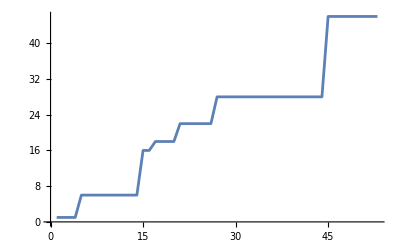

```mathematica
ListLinePlot[Rest@FoldList[Max,First[list],Rest[list]],ImageSize->Full]
```

Make a list for the first 1000 numbers.

```mathematica
list=RationalNumberRepeatingDecimalPeriod[Array[1/#&,1000,2]];
```

```mathematica
runningMaximum=Rest@FoldList[Max,First[list],Rest[list]];
```

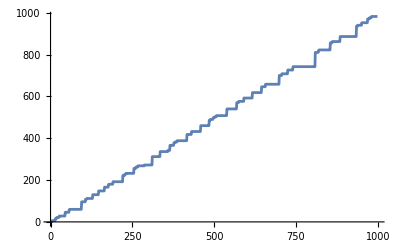

```mathematica
ListLinePlot[Rest@FoldList[Max,First[list],Rest[list]],ImageSize->Full]
```

Related Guides

Combinatorics

Functions I Understand in combinatorics

Related Tech Notes

## Metadata

### Categorization

Tech Note

PeterBurbery/Combinatorics

PeterBurbery`Combinatorics`

PeterBurbery/Combinatorics/tutorial/Combinatorics

### Keywords